### Tarea II Error Cuadratico Medio

```mathematica
-Graphics--Graphics-
```

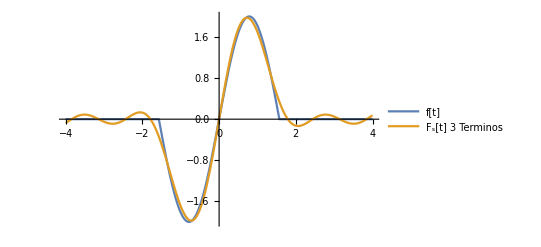

f(t)= -A HeavisideTheta[-π/2+t] Sin[2 t]+A HeavisideTheta[π/2+t] Sin[2 t]
a_0=0
a_n= 0
b_0= -(4 A Sin[(n π)/2])/((-4+n^2) π)
F_s(t)= (4 A Sin[t])/(3 π)+A Cos[t] Sin[t]+(4 A Sin[3 t])/(5 π)  ; 3 terminos
E_k= 0.00251395 A^2

```mathematica
Clear["Global`*"]
T=2Pi;
f=(A*Sin[2t]-0)*HeavisideTheta[t-(-Pi/2)] +(0-A*Sin[2t])*HeavisideTheta[t-(Pi/2)];
Subscript[a, 0]=(2/T)*Integrate[f,{t,-T/2,T/2}];
Subscript[a, N]=(2/T)*Integrate[f*Cos[(2*Pi*n*t)/T],{t,(-T/2),(T/2)}];
Subscript[b, N]=(2/T)*Integrate[f*Sin[(2*Pi*n*t)/T],{t,(-T/2),(T/2)}];
Fs=(Subscript[a, 0]/2)+Sum[Limit[Subscript[a, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,3}]+Sum[Limit[(Subscript[b, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,3}]
EK=(1/T)*Integrate[(f-Fs)^2,{t,(-T/2),(T/2)}]//N;
Plot[{f/.A->2,Fs/.A->2},{t,-4,4},PlotRange->All,PlotLegends->{"f[t]","F_s[t] 3 Terminos"}]
Print["f(t)= ",f,"\na_0=",Subscript[a, 0],"\na_n= ",Subscript[a, N],"\nb_0= ",Subscript[b, N],"\nF_s(t)= ",Fs,"  ; 3 terminos\nE_k= ",EK]
```

### Ejercicio 1

f(t)= HeavisideTheta[t]+HeavisideTheta[t-T]-2 HeavisideTheta[t-T/2]
a_0=0
a_n= (2 Sin[n π]-Sin[2 n π])/(n π)
b_0= -(4 Cos[n π] Sin[(n π)/2]^2)/(n π)
F_s(t)= (4 (3 Sin[(2 π t)/T]+Sin[(6 π t)/T]))/(3 π)  ; 3 terminos
E_k= 0.0993673

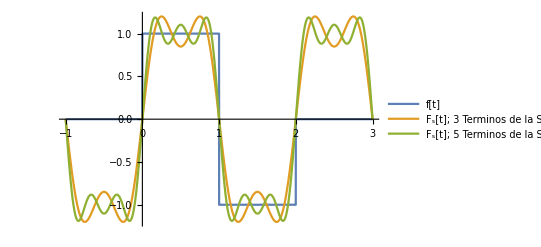

```mathematica
Clear["Global`*"]
f=(1-0)HeavisideTheta[t-0]+(-1-(1))HeavisideTheta[t-(T/2)]+(0-(-1))HeavisideTheta[t-T];
Subscript[A, 0]=(2/T)(Integrate[(1),{t,0,T/2}]+Integrate[(-1),{t,(T/2),T}]);
Subscript[A, N]=Simplify[(2/T)(Integrate[(1)*Cos[(2*Pi*n*t)/T],{t,0,T/2}]+Integrate[(-1)Cos[(2*Pi*n*t)/T],{t,(T/2),T}]),n ϵ Integers];
Subscript[B, N]=Simplify[(2/T)(Integrate[(1)*Sin[(2*Pi*n*t)/T],{t,0,T/2}]+Integrate[(-1)Sin[(2*Pi*n*t)/T],{t,(T/2),T}]),n ϵ Integers && n≥1];
Fs=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,3}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,3}],n ϵ Integers && n≥0];
Fs5=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,5}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,5}],n ϵ Integers && n≥0];
Subscript[E, K]=Simplify[(1/T)*Integrate[((f-Fs)^2),{t,0,T}],T∈Reals && T>0]//N;
Print["f(t)= ",f,"\na_0=",Subscript[A, 0],"\na_n= ",Subscript[A, N],"\nb_0= ",Subscript[B, N],"\nF_s(t)= ",Fs,"  ; 3 terminos\nE_k= ",Subscript[E, K]]
Plot[{f/.T->2,Fs/.T->2,Fs5/.T->2},{t,-1,3},PlotRange->All,PlotLegends->{"f[t]","F_s[t]; 3 Terminos de la Serie","F_s[t]; 5 Terminos de la Serie"}]
```

### Ejercicio 2

f(t)= HeavisideTheta[-(3 π)/2+t]-2 HeavisideTheta[-π/2+t]+HeavisideTheta[π/2+t]
a_0=0
a_n= (4 Sin[(n π)/2]^3)/(n π)
b_0= -(2 Sin[(n π)/2] Sin[n π])/(n π)
F_s(t)= -(4 (-3 Cos[t]+Cos[3 t]))/(3 π)  ; 3 terminos
E_k= 0.0993673

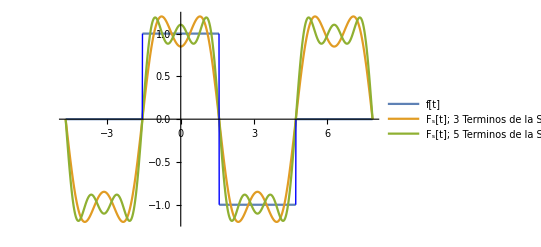

```mathematica
Clear["Global`*"]
f=(1-0)HeavisideTheta[t-(-Pi/2)]+(-1-(1))HeavisideTheta[t-(Pi/2)]+(0-(-1))HeavisideTheta[t-(3Pi/2)];
T=2Pi;
Subscript[A, 0]=(2/T)(Integrate[(1),{t,-Pi/2,Pi/2}]+Integrate[(-1),{t,(Pi/2),(3Pi/2)}]);
Subscript[A, N]=Simplify[(2/T)(Integrate[(1)*Cos[(2*Pi*n*t)/T],{t,-Pi/2,Pi/2}]+Integrate[(-1)Cos[(2*Pi*n*t)/T],{t,(Pi/2),(3Pi/2)}]),n ϵ Integers];
Subscript[B, N]=Simplify[(2/T)(Integrate[(1)*Sin[(2*Pi*n*t)/T],{t,-Pi/2,Pi/2}]+Integrate[(-1)Sin[(2*Pi*n*t)/T],{t,(Pi/2),(3Pi/2)}]),n ϵ Integers && n≥1];
Fs=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,3}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,3}],n ϵ Integers && n≥0];
Fs5=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,5}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,5}],n ϵ Integers && n≥0];
Subscript[E, K]=Simplify[(1/T)*Integrate[((f-Fs)^2),{t,-Pi/2,3Pi/2}],T∈Reals && T>0]//N;
Print["f(t)= ",f,"\na_0=",Subscript[A, 0],"\na_n= ",Subscript[A, N],"\nb_0= ",Subscript[B, N],"\nF_s(t)= ",Fs,"  ; 3 terminos\nE_k= ",Subscript[E, K]]
Plot[{f,Fs,Fs5},{t,-3Pi/2,5Pi/2},PlotRange->All,PlotLegends->{"f[t]","F_s[t]; 3 Terminos de la Serie","F_s[t]; 5 Terminos de la Serie"},ExclusionsStyle->Blue]
```

### Ejercicio 3

f(t)= -A HeavisideTheta[-1/2000000+t]+A HeavisideTheta[t]
a_0=A
a_n= (A Sin[n π])/(n π)
b_0= (2 A Sin[(n π)/2]^2)/(n π)
F_s(t)= (A (3 π+12 Sin[2000000 π t]+4 Sin[6000000 π t]))/(6 π)  ; 3 terminos
E_k= 0.0248418 A^2

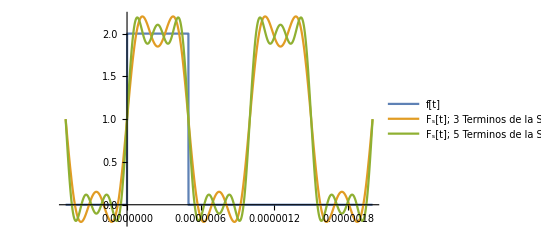

```mathematica
Clear["Global`*"]
f=(A-0)HeavisideTheta[t-(0)]+(0-(A))HeavisideTheta[t-(T/2)];
T=1*10^-6;
Subscript[A, 0]=(2/T)(Integrate[(A),{t,0,T/2}]+Integrate[(0),{t,(T/2),(T)}]);
Subscript[A, N]=Simplify[(2/T)(Integrate[(A)*Cos[(2*Pi*n*t)/T],{t,0,T/2}]+Integrate[(0)Cos[(2*Pi*n*t)/T],{t,(T/2),(T)}]),n ϵ Integers];
Subscript[B, N]=Simplify[(2/T)(Integrate[(A)*Sin[(2*Pi*n*t)/T],{t,0,T/2}]+Integrate[(0)Sin[(2*Pi*n*t)/T],{t,(T/2),(T)}]),n ϵ Integers && n≥1];
Fs=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,3}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,3}],n ϵ Integers && n≥0];
Fs5=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,5}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,5}],n ϵ Integers && n≥0];
Subscript[E, K]=Simplify[(1/T)*Integrate[((f-Fs)^2),{t,0,T}],T∈Reals && T>0]//N;
Print["f(t)= ",f,"\na_0=",Subscript[A, 0],"\na_n= ",Subscript[A, N],"\nb_0= ",Subscript[B, N],"\nF_s(t)= ",Fs,"  ; 3 terminos\nE_k= ",Subscript[E, K]]
Plot[{f/.A->2,Fs/.A->2,Fs5/.A->2},{t,-T/2,4T/2},PlotRange->All,PlotLegends->{"f[t]","F_s[t]; 3 Terminos de la Serie","F_s[t]; 5 Terminos de la Serie"}]
```

### Ejercicio 4

f(t)= (A t HeavisideTheta[t])/π+(A (-2 π+t) HeavisideTheta[-2 π+t])/π+(-(A t)/π-(A (-2 π+t))/π) HeavisideTheta[-π+t]
a_0=A
a_n= (4 A Cos[n π] Sin[(n π)/2]^2)/(n^2 π^2)
b_0= (A (2 Sin[n π]-Sin[2 n π]))/(n^2 π^2)
F_s(t)= (A (9 π^2-72 Cos[t]-8 Cos[3 t]))/(18 π^2)  ; 3 terminos
E_k= 0.000191551 A^2

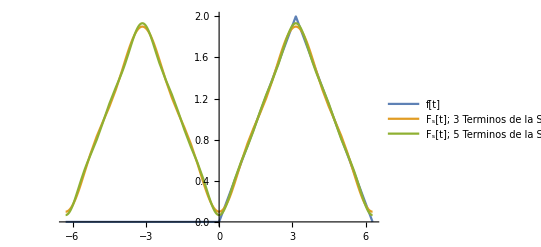

```mathematica
Clear["Global`*"]
f=((A*t/Pi)-0)HeavisideTheta[t-(0)]+((-A*(t-2Pi)/Pi)-(A*t/Pi))HeavisideTheta[t-(Pi)]+(0-(-A*(t-2Pi)/Pi))HeavisideTheta[t-(2Pi)];
T=2Pi;
Subscript[A, 0]=(2/T)(Integrate[(A*t/Pi),{t,0,Pi}]+Integrate[(-A*(t-2Pi)/Pi),{t,Pi,(2Pi)}]);
Subscript[A, N]=Simplify[(2/T)(Integrate[(A*t/Pi)*Cos[(2*Pi*n*t)/T],{t,0,Pi}]+Integrate[(-A*(t-2Pi)/Pi)Cos[(2*Pi*n*t)/T],{t,(Pi),(2Pi)}]),n ϵ Integers];
Subscript[B, N]=Simplify[(2/T)(Integrate[(A*t/Pi)*Sin[(2*Pi*n*t)/T],{t,0,Pi}]+Integrate[(-A*(t-2Pi)/Pi)Sin[(2*Pi*n*t)/T],{t,(Pi),(2Pi)}]),n ϵ Integers];
Fs=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,3}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,3}],n ϵ Integers && n≥0];
Fs5=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,5}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,5}],n ϵ Integers && n≥0];
Subscript[E, K]=Simplify[(1/T)*Integrate[((f-Fs)^2),{t,0,T}],T∈Reals && T>0]//N;
Print["f(t)= ",f,"\na_0=",Subscript[A, 0],"\na_n= ",Subscript[A, N],"\nb_0= ",Subscript[B, N],"\nF_s(t)= ",Fs,"  ; 3 terminos\nE_k= ",Subscript[E, K]]
Plot[{f/.A->2,Fs/.A->2,Fs5/.A->2},{t,-2Pi,2Pi},PlotRange->All,PlotLegends->{"f[t]","F_s[t]; 3 Terminos de la Serie","F_s[t]; 5 Terminos de la Serie"}]
```

### Ejercicio 5

f(t)= (A t HeavisideTheta[t])/(2 π)-(A t HeavisideTheta[-2 π+t])/(2 π)
a_0=A
a_n= (A (2 n π Cos[n π]-Sin[n π]) Sin[n π])/(n^2 π^2)
b_0= (A (-2 n π Cos[2 n π]+Sin[2 n π]))/(2 n^2 π^2)
F_s(t)= -(A (-3 π+6 Sin[t]+3 Sin[2 t]+2 Sin[3 t]))/(6 π)  ; 3 terminos
E_k= 0.0143786 A^2

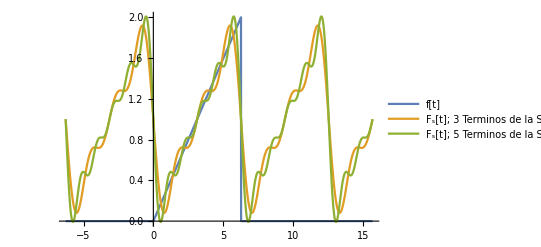

```mathematica
Clear["Global`*"]
f=((A*t/(2Pi))-0)HeavisideTheta[t-(0)]+((0)-(A*t/(2Pi)))HeavisideTheta[t-(2Pi)];
T=2Pi;
Subscript[A, 0]=(2/T)(Integrate[(A*t/(2Pi)),{t,0,2Pi}]);
Subscript[A, N]=Simplify[(2/T)(Integrate[(A*t/(2Pi))*Cos[(2*Pi*n*t)/T],{t,0,2Pi}]),n ϵ Integers];
Subscript[B, N]=Simplify[(2/T)(Integrate[(A*t/(2Pi))*Sin[(2*Pi*n*t)/T],{t,0,2Pi}]),n ϵ Integers];
Fs=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,3}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,3}],n ϵ Integers && n≥0];
Fs5=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,5}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,5}],n ϵ Integers && n≥0];
Subscript[E, K]=Simplify[(1/T)*Integrate[((f-Fs)^2),{t,0,2Pi}],T∈Reals && T>0]//N;
Print["f(t)= ",f,"\na_0=",Subscript[A, 0],"\na_n= ",Subscript[A, N],"\nb_0= ",Subscript[B, N],"\nF_s(t)= ",Fs,"  ; 3 terminos\nE_k= ",Subscript[E, K]]
Plot[{f/.A->2,Fs/.A->2,Fs5/.A->2},{t,-2Pi,5Pi},PlotRange->All,PlotLegends->{"f[t]","F_s[t]; 3 Terminos de la Serie","F_s[t]; 5 Terminos de la Serie"}]
```

### Ejercicio 6

f(t)= A HeavisideTheta[t]+A HeavisideTheta[-2 π+t]-2 A HeavisideTheta[-π+t]
a_0=0
a_n= (A (2 Sin[n π]-Sin[2 n π]))/(n π)
b_0= (A (1-2 Cos[n π]+Cos[2 n π]))/(n π)
F_s(t)= (4 A (3 Sin[t]+Sin[3 t]))/(3 π)  ; 3 terminos
E_k= 0.0993673 A^2

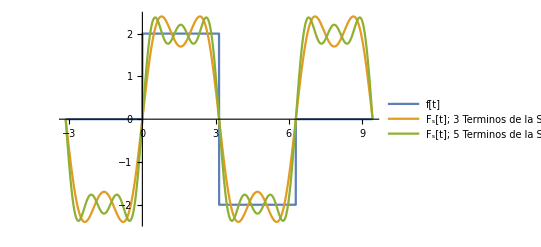

```mathematica
Clear["Global`*"]
T=2Pi;
f=(A-0)HeavisideTheta[t-0]+(-A-(A))HeavisideTheta[t-(T/2)]+(0-(-A))HeavisideTheta[t-T];
Subscript[A, 0]=(2/T)(Integrate[(A),{t,0,T/2}]+Integrate[(-A),{t,(T/2),T}]);
Subscript[A, N]=Simplify[(2/T)(Integrate[(A)*Cos[(2*Pi*n*t)/T],{t,0,T/2}]+Integrate[(-A)Cos[(2*Pi*n*t)/T],{t,(T/2),T}]),n ϵ Integers];
Subscript[B, N]=Simplify[(2/T)(Integrate[(A)*Sin[(2*Pi*n*t)/T],{t,0,T/2}]+Integrate[(-A)Sin[(2*Pi*n*t)/T],{t,(T/2),T}]),n ϵ Integers && n≥1];
Fs=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,3}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,3}],n ϵ Integers && n≥0];
Fs5=Simplify[(Subscript[A, 0]/2)+Sum[Limit[Subscript[A, N]*Cos[(2*Pi*n*t)/T],n->k],{k,1,5}]+Sum[Limit[(Subscript[B, N]*Sin[(2*Pi*n*t)/T]),n->k],{k,1,5}],n ϵ Integers && n≥0];
Subscript[E, K]=Simplify[(1/T)*Integrate[((f-Fs)^2),{t,0,T}],T∈Reals && T>0]//N;
Print["f(t)= ",f,"\na_0=",Subscript[A, 0],"\na_n= ",Subscript[A, N],"\nb_0= ",Subscript[B, N],"\nF_s(t)= ",Fs,"  ; 3 terminos\nE_k= ",Subscript[E, K]]
Plot[{f/.A->2,Fs/.A->2,Fs5/.A->2},{t,-Pi,3Pi},PlotRange->All,PlotLegends->{"f[t]","F_s[t]; 3 Terminos de la Serie","F_s[t]; 5 Terminos de la Serie"}]
```